```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
tableOutFunc2[dataIn_, tit_]:=Module[{ts,dataN,out},
ts=Keys[dataIn];
dataN=Map[Function[x,Prepend[

Map[Function[y,StringReplace[ToString[y],{"{}"->"-","{"->"(","}"->")"}] ],Values[dataIn][[x]]]

,ts[[x]]]], Range[Length[dataIn]]];

out=Text@Grid[
Prepend[Prepend[dataN,{" ", "DOJ","Z","F"}],{tit}],
Background->{None,{Lighter[Yellow,.9],Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Lighter[Gray,.5],Darker[Gray,.6],{False},Darker[Gray,.6]}}, 
Alignment->{{Center,Center}},ItemSize->{{3,32,32,32}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}];

Return[out];
];
```

```mathematica
accEVBK=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/POINTS/gdc_VER_EVBK_points.txt"];
accCH=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/CH/gdc_VER_CH_points.txt"];
confVal=Get["/home/carla/GDC/CH_Pool/VV_Tables/THRE_RATIO_TIME.txt"];
names=Keys[accEVBK]
confs={"DOJ","Z","F"};
timesteps=Range[17];
col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]];
homeAdd="/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/";
spezAdd="CONF_VV/RESULTS/";
plotType="R";
revType="ALL";
```

{DLB,MUR,LYE,PHI,SED,AUS}

```mathematica
dataTableDOJ=circTableDataFunc[confVal,"DOJ",names, revType];
dataTableZ=circTableDataFunc[confVal,"Z",names,revType];
dataTableF=circTableDataFunc[confVal,"F",names,revType];
dataAll=Merge[{dataTableDOJ,dataTableZ,dataTableF},Identity]
```

<|0b→{{},{},{}},1a→{{},{},{}},1b→{{},{},{}},2a→{{},{},{}},2b→{{},{},{}},3a→{{},{},{}},3b→{{},{},{}},4a→{{},{(DLB, 0.56)},{(DLB, 0.56)}},4b→{{(PHI, 0.7)},{(PHI, 1.)},{(PHI, 1.)}},5a→{{(MUR, 0.61),(PHI, 0.73)},{(DLB, 1.),(MUR, 0.69),(LYE, 1.),(PHI, 1.)},{(MUR, 0.69),(LYE, 1.),(PHI, 1.)}},5b→{{(MUR, 0.51),(PHI, 0.7)},{(MUR, 0.89),(PHI, 1.)},{(MUR, 0.89),(PHI, 1.)}},6a→{{(MUR, 0.51),(PHI, 0.7)},{(MUR, 0.89),(LYE, 1.),(PHI, 1.)},{(MUR, 0.89),(PHI, 1.)}},6b→{{(LYE, 0.67),(PHI, 0.7),(AUS, 0.73)},{(LYE, 1.),(PHI, 1.),(AUS, 1.)},{(LYE, 1.),(PHI, 1.),(AUS, 1.)}},7a→{{(LYE, 0.67),(PHI, 0.7),(AUS, 0.73)},{(LYE, 1.),(PHI, 1.),(AUS, 1.)},{(LYE, 1.),(PHI, 1.),(AUS, 1.)}},7b→{{(MUR, 1.),(LYE, 1.),(PHI, 1.),(AUS, 1.)},{(MUR, 1.),(LYE, 1.),(PHI, 1.),(AUS, 1.)},{(MUR, 1.),(LYE, 1.),(PHI, 1.),(AUS, 1.)}},8a→{{(MUR, 1.),(PHI, 1.),(AUS, 1.)},{(MUR, 1.),(PHI, 1.),(AUS, 1.)},{(MUR, 1.),(PHI, 1.),(AUS, 1.)}},8b→{{(DLB, 1.),(MUR, 1.),(LYE, 1.),(PHI, 1.),(SED, 1.),(AUS, 1.)},{(DLB, 1.),(MUR, 1.),(LYE, 1.),(PHI, 1.),(SED, 1.),(AUS, 1.)},{(DLB, 1.),(MUR, 1.),(LYE, 1.),(PHI, 1.),(SED, 1.),(AUS, 1.)}}|>

```mathematica
tab=tableOutFunc2[dataAll, revType]
```

ALL |  |  | 
  | DOJ | Z | F
0b | - | - | -
1a | - | - | -
1b | - | - | -
2a | - | - | -
2b | - | - | -
3a | - | - | -
3b | - | - | -
4a | - | ((DLB, 0.56)) | ((DLB, 0.56))
4b | ((PHI, 0.7)) | ((PHI, 1.)) | ((PHI, 1.))
5a | ((MUR, 0.61), (PHI, 0.73)) | ((DLB, 1.), (MUR, 0.69), (LYE, 1.), (PHI, 1.)) | ((MUR, 0.69), (LYE, 1.), (PHI, 1.))
5b | ((MUR, 0.51), (PHI, 0.7)) | ((MUR, 0.89), (PHI, 1.)) | ((MUR, 0.89), (PHI, 1.))
6a | ((MUR, 0.51), (PHI, 0.7)) | ((MUR, 0.89), (LYE, 1.), (PHI, 1.)) | ((MUR, 0.89), (PHI, 1.))
6b | ((LYE, 0.67), (PHI, 0.7), (AUS, 0.73)) | ((LYE, 1.), (PHI, 1.), (AUS, 1.)) | ((LYE, 1.), (PHI, 1.), (AUS, 1.))
7a | ((LYE, 0.67), (PHI, 0.7), (AUS, 0.73)) | ((LYE, 1.), (PHI, 1.), (AUS, 1.)) | ((LYE, 1.), (PHI, 1.), (AUS, 1.))
7b | ((MUR, 1.), (LYE, 1.), (PHI, 1.), (AUS, 1.)) | ((MUR, 1.), (LYE, 1.), (PHI, 1.), (AUS, 1.)) | ((MUR, 1.), (LYE, 1.), (PHI, 1.), (AUS, 1.))
8a | ((MUR, 1.), (PHI, 1.), (AUS, 1.)) | ((MUR, 1.), (PHI, 1.), (AUS, 1.)) | ((MUR, 1.), (PHI, 1.), (AUS, 1.))
8b | ((DLB, 1.), (MUR, 1.), (LYE, 1.), (PHI, 1.), (SED, 1.), (AUS, 1.)) | ((DLB, 1.), (MUR, 1.), (LYE, 1.), (PHI, 1.), (SED, 1.), (AUS, 1.)) | ((DLB, 1.), (MUR, 1.), (LYE, 1.), (PHI, 1.), (SED, 1.), (AUS, 1.))

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType];
Export[revType<>"_table.jpeg",tab,ImageResolution->200]
```

ALL_table.jpeg

```mathematica
(* Dec>0.01 *)
dataDOJ=sumUpFunc[accEVBK, accCH,confVal,"DOJ",names,revType];
dataZ=sumUpFunc[accEVBK, accCH,confVal,"Z",names, revType];
dataF=sumUpFunc[accEVBK, accCH,confVal,"F",names, revType];
```

```mathematica
dataDOJ[[3]][[1]][[2]]
```

{{0.519231,0.6,1},{0.423077,0.6,2},{0.533333,0.6,3},{0.6,0.6,4},{0.771429,0.6,5},{0.77551,0.6,6},{0.938776,0.6,7},{0.906977,0.6,8},{0.911602,0.533333,9},{0.879581,0.533333,10},{0.889447,0.533333,11},{0.881517,0.533333,12},{0.807175,0.6,13},{0.778723,0.6,14},{0.76569,0.6,15},{0.764259,0.6,16},{0.9631,1.,17}}

```mathematica
shrinkFac1=0.07;
shrinkFac2=0.07;
plotsDOJ=Map[singlePlot[#, dataDOJ,col2,shrinkFac1,shrinkFac2,plotType]&,names];
gridDOJ=Grid[{plotsDOJ[[1;;2]],plotsDOJ[[3;;4]],plotsDOJ[[5;;6]]}];
plotsZ=Map[singlePlot[#, dataZ,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridZ=Grid[{plotsZ[[1;;2]],plotsZ[[3;;4]],plotsZ[[5;;6]]}];
plotsF=Map[singlePlot[#, dataF,col2,shrinkFac1,shrinkFac2, plotType]&,names];
gridF=Grid[{plotsF[[1;;2]],plotsF[[3;;4]],plotsF[[5;;6]]}];
```

size {0.07}

size {0.0355266,0.0225168,0.0225168,0.07,0.07,0.07}

size {0.0416174,0.0416174,0.07,0.07}

size {0.0450328,0.0482892,0.0450328,0.0450328,0.0450328,0.0450328,0.07,0.07,0.07}

size {0.07}

size {0.0482892,0.0482892,0.07,0.07,0.07}

size {0.0294127,0.07,0.07}

size {0.0437715,0.0617552,0.0617552,0.07,0.07,0.07}

size {0.07,0.07,0.07,0.07,0.07,0.07}

size {0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07}

size {0.07}

size {0.07,0.07,0.07,0.07,0.07}

size {0.0294127,0.07}

size {0.0437715,0.0617552,0.0617552,0.07,0.07,0.07}

size {0.07,0.07,0.07,0.07,0.07}

size {0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07,0.07}

size {0.07}

size {0.07,0.07,0.07,0.07,0.07}

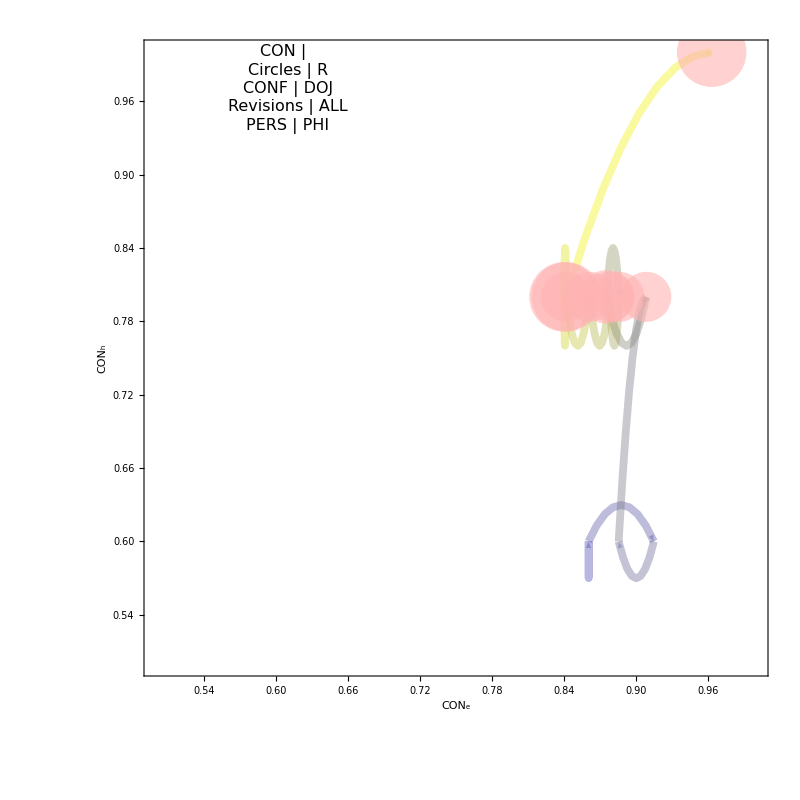
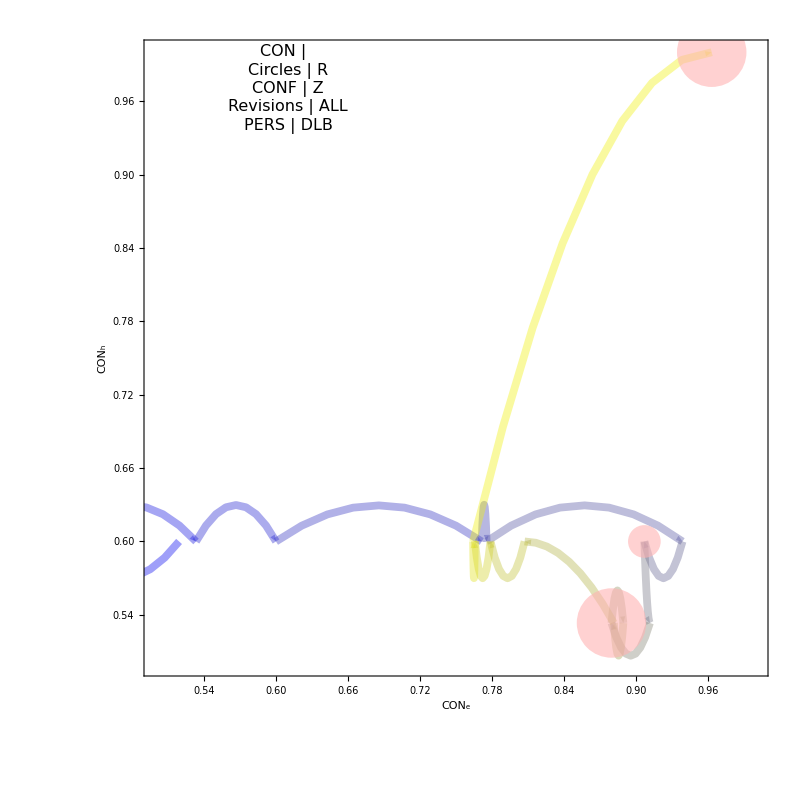

```mathematica
{plotsDOJ[[4]],plotsZ[[1]]}
```

```mathematica
SetDirectory[homeAdd<>spezAdd<>revType]

Export[ToString[plotType]<>"_DOJ.jpeg",gridDOJ]
Export[ToString[plotType]<>"_Z.jpeg",gridZ]
Export[ToString[plotType]<>"_F.jpeg",gridF]
```

/home/carla/GDC/Comparisons/New_REKO_19_02_21/Bridge/CONF_VV/RESULTS/ALL

R_DOJ.jpeg

R_Z.jpeg

R_F.jpeg